```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\tonnam_backup\Research_scratch\flux_pmf\PVP10_atac\100Ag\PT_eq\8_Try\1_Restart

```mathematica
thermo=Range[32];
```

```mathematica
For[i=0,i<32,i++,
log=OpenRead[StringJoin["thermo.lammps.",ToString[9*i+413]]];
Find[log,"# Step PotEng"];thermo[[i+1]]=ReadList[log,{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
]
```

```mathematica
between413=Boole[NonNegative[Boole[NonNegative[thermo[[All,All,5]]-410]]+Boole[Negative[thermo[[All,All,5]]-416]]-2]];
(*Pick datapoints where T is between 410-416 K*)
```

```mathematica
between413pick=Reap[For[i=1,i≤32,i++,
Sow[Transpose[Table[between413[[i]],{12}]]];
]][[2,1]];
(*Duplicate each element 12 times for function Pick[]*)
```

```mathematica
poteng=Reap[For[i=1,i≤32,i++,
Sow[Partition[Flatten[Pick[thermo[[i]],between413pick[[i]],1]],12]];
]][[2,1]];
(*Use Pick[] on thermo*)
```

```mathematica
starttime=thermo[[1,1,1]];
```

```mathematica
plotpoteng=Reap[For[i=1,i≤32,i++,
Sow[Partition[Riffle[poteng[[i,All,1]]-starttime,poteng[[i,All,2]]],2]];
]][[2,1]];
(*Format data for ListPlot[]*)
```

```mathematica
starttime
```

33820010

```mathematica
plotpoteng
```

{{{173540,-2081.51},{177750,-2083.52},{177800,-2085.39},{177850,-2085.18},{177930,-2081.94},{178220,-2086.4},{178240,-2088.96},{178270,-2091.99},{178300,-2092.18},{178310,-2091.68},«236»,{455150,-2080.39},{455500,-2090.03},{455550,-2090.94},{455570,-2088.86},{455600,-2089.},{455610,-2088.09},{455620,-2088.34},{455640,-2084.83},{455650,-2083.84},{455670,-2080.47}},«30»,{«1»}}

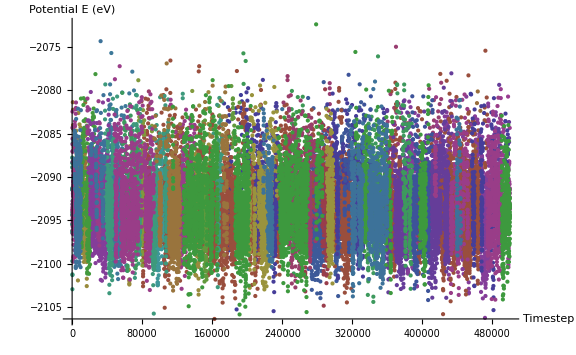

```mathematica
graph=ListPlot[Select[plotpoteng,UnsameQ[#,{}]&],AxesLabel->{"Timestep","Potential E (eV)"},LabelStyle->Directive[FontSize->15],ImageSize->Large]
```

```mathematica
CreateDirectory["graphs"];
Export["graphs/PotentialE.png",graph,ImageResolution->500];
```

CreateDirectory::filex: "D:\\tonnam_backup\\Research_scratch\\flux_pmf\\PVP10_atac\\100Ag\\PT_eq\\8_Try\\1_Restart\\graphs\\" already exists.